```mathematica
f[t_,t0_,w_,s_]=Integrate[Exp[-(T-t0)^2 / s^2]*Cos[w*T],{T,0,t}]
```

1/4 ⅇ^(-1/4 w (4 ⅈ t0+s^2 w)) √π s (Erf[t0/s-(ⅈ s w)/2]+Erf[(t-t0)/s+(ⅈ s w)/2]+ⅇ^(2 ⅈ t0 w) (Erf[(t-t0)/s-(ⅈ s w)/2]+Erf[t0/s+(ⅈ s w)/2]))

```mathematica
Erf[4+2I]
```

Erf[4+2 ⅈ]

```mathematica
a=0.4;
b=0.9;
N[Erf[a+b* ⅈ]]
N[Re[Erf[a+b* ⅈ]+Erf[a-b* ⅈ]] / Re[Erf[a+b* ⅈ]]]
N[Im[Erf[a+b* ⅈ]+Erf[a-b* ⅈ]] ]
N[Erf[a]]
```

0.885283+1.04796 ⅈ

2.

0.

0.428392

```mathematica
g[Ta_,asa_, ωa_, ta_, za_, τa_]=Exp[-(Ta-τa)^2 / asa +I*ωa*Ta];
gRaw[Ta_,wa_, ωa_, ta_, za_]=Exp[-(za-β*cLight*(ta-Ta))^2/wa^2]*Exp[I*ωa*Ta];
gIntegral[asa_, ωa_, ta_, za_, τa_]=Refine[Integrate[g[Ta,asa, ωa, ta, za, τa],{Ta,-Infinity,ta}],za∈Reals && ωa∈Reals && ta∈Reals && Re[asa]>0];
gRawIntegral[wa_, ωa_, ta_, za_] = Refine[Integrate[gRaw[Ta,wa, ωa, ta, za],{Ta,-Infinity,ta}],za∈Reals && ωa∈Reals && ta∈Reals && wa∈Reals]
```

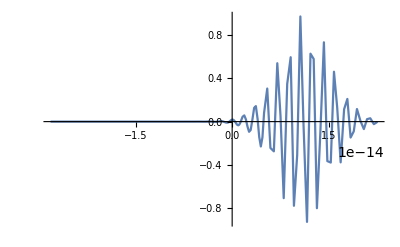

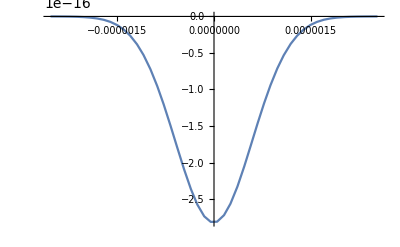

-Graphics-

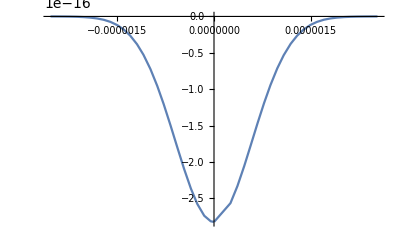

```mathematica
tz[z_]=z / (β * cLight);
l = 532*10^-9;
ω=cLight * 2*Pi / l;
x0=0;
y0=0;
t0=tz[4*w0];
z0=2*w0;
Na = 0.2;
β = 0.5;
w0 = l / (Pi * Na);
as = (w0 /( β*cLight))^2;
cLight = 299792458;
τ[ta_, za_] = ta-za / (β*cLight);

Plot[Re[g[T,as, ω, t0, z0, τ[t0,z0]]],{T,tz[-5*w0],t0}, PlotRange->Full]
Plot[Re[gIntegral[as, ω, t0, z, τ[t0,z]]],{z,-3w0,3w0}, PlotRange->Full]
Plot[Re[gRaw[T,w0, ω, t0, z0]],{T,tz[-5*w0],t0}, PlotRange->Full]
Plot[Re[gRawIntegral[w0, ω, t0, z]],{z,-3w0,3w0}, PlotRange->Full]
```

```mathematica
z0=0
N[gIntegral[as, ω, t0, z0, τ[t0,z0]]]
N[ω]
as
w0
```

0

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

3.5407×10^15

3.19067×10^-29

8.46704×10^-7

```mathematica
g2[T_,a_,σ_]=Exp[-(T-a)^2 / σ^2]
Simplify[Refine[Integrate[g2[T,a,σ],{T,-Infinity,t}],Re[σ^2>0]]]
```

ⅇ^(-(-a+T)^2/σ^2)

ConditionalExpression[1/2 √π (1/(√(1/σ^2))-σ Erf[(a-t)/σ]), (Re[a/σ^2]<0||Re[σ^2]>0)&&Re[σ^2]≥0]

```mathematica
g3[T_,a_,b_,,c_]=Exp[(T-b)/a]
Refine[Integrate[g[T,a,b,bi,c],{T,-Infinity,t}],Re[]]
```